## Two-state mixing

```mathematica
(*The interaction strength between the two states*)
VINT=0.05;
(*The initial separation between the two states*)
DE21=0.1;
RR[de21_,vint_]:=de21/vint;
(*the smaller mixing amplitude β*)
β[r_]:=1/((1+(r/2+Sqrt[1+r^2/4])^2)^(1/2));
Eshift[r_,initialSpacing_]:=1/2(Sqrt[1+4/r^2]-1)*initialSpacing;
```

#### Numerical test

```mathematica
initialSpacing=70;
interaction=20;
rvalue=N[initialSpacing/interaction]
Eshift[rvalue,initialSpacing]
percentageOfMixing=(Eshift[rvalue,initialSpacing]/initialSpacing)*100
β[rvalue]
```

3.5

5.31129

7.58756

0.256668

## Find the inverse of the function β(R)

```mathematica
invbeta[x_]:=InverseFunction[ConditionalExpression[1/((1+(#/2+Sqrt[1+#^2/4])^2)^(1/2)),0.01<#1<12]&][x];
```

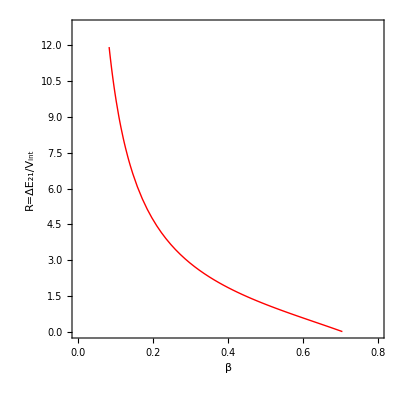

```mathematica
Plot[invbeta[x],{x,0.083,0.705},PlotRange->{{0,0.8},{0,12.8}},AspectRatio->1,Frame->True,Axes->False,FrameLabel->{"β","R=ΔE_21/V_int"},PlotStyle->{Thick,Red},FrameStyle->Directive[Black,Thick],LabelStyle->{19,Bold,Black,FontFamily->"Times"}]
```

```mathematica
invbeta[x]
```

ConditionalExpression[√((-1.+4. x^2-4. x^4)/(x^2 (-1.+x^2))), 0.0824805<x<0.705337]

## Find the inverse of the energy shift for the mixed states

```mathematica
(*this is in units of the unperturbed shift*)
invshift[x_]:=InverseFunction[ConditionalExpression[1/2(Sqrt[1+4/#^2]-1),0.01<#1<12]&][x];
invshift[x]
```

ConditionalExpression[√(1/(x+x^2)), 0.00689688<x<99.5012]

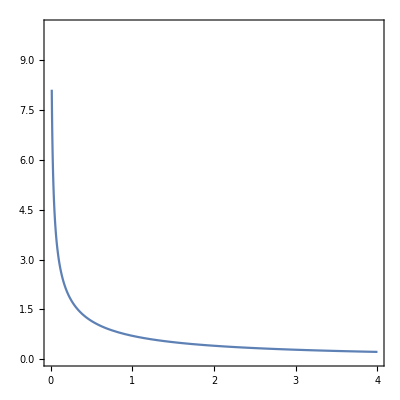

```mathematica
Plot[{invshift[shift]},{shift,0.015,4},PlotRange->{0,10},AspectRatio->1,Frame->True,Axes->False]
```

```mathematica
N[1/2(Sqrt[1+4/10^2]-1)]
```

0.00990195